```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[2,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[1/1000,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =2; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 15125.9

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=25;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
ϵpp[k0_]=SetPrecision[2.22,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[2.49,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика в эВ: ",qc mee]
Print["Толщина пластины холестерика в мкм: ",Lz lc 10^4]
Print["Анизотропия de: ",dec[1.5/mee]]
```

Волновой вектор холестерика в эВ: 0.774583

Толщина пластины холестерика в мкм: 20.

Анизотропия de: 0.121622

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,xms2,xpsm4,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
xms2=0;xpsm4=0;(*зануляем высшие поправки*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,yms2,ypsm4,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
yms2=0;ypsm4=0;(*зануляем высшие поправки*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

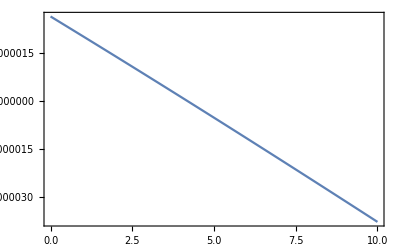
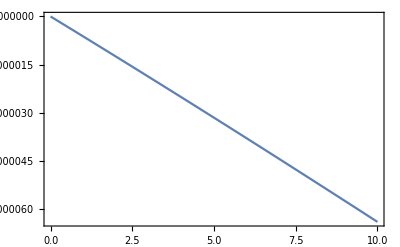
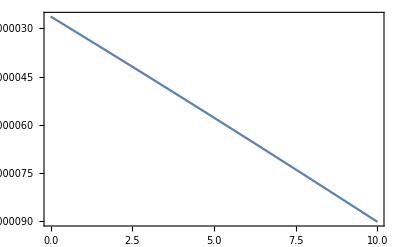
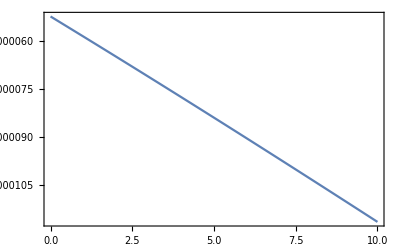

```mathematica
(*-------примеры оптический диапозон 1-4 эВ-------*)
{Plot[EqnSpecX[xx/mee,1/5,-2],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,0],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,1],{xx,0,10},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/5,-2],{xx,4}]
```

{xx→4.17512}

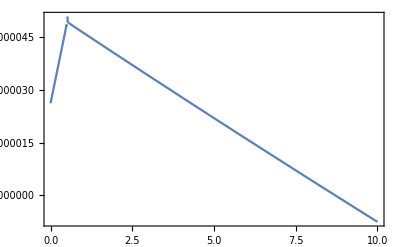
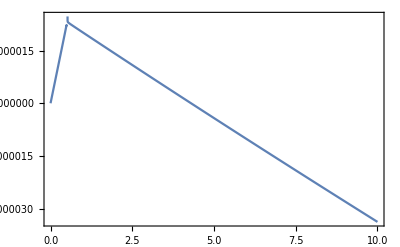
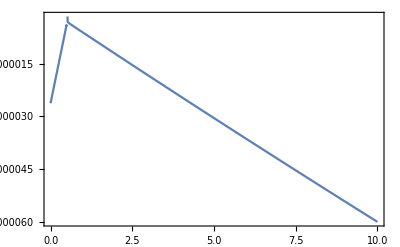
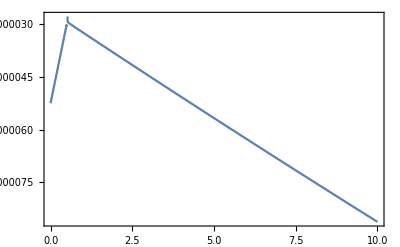

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,0,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,0,10},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/5,-2],{xx,9}]
FindRoot[EqnSpecY[xx/mee,1/5,-1],{xx,4}]
```

{xx→8.71523}

{xx→4.29774}

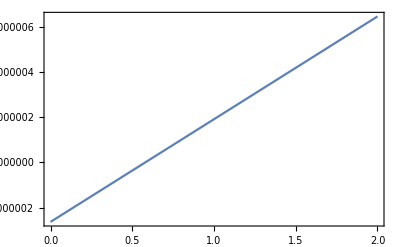
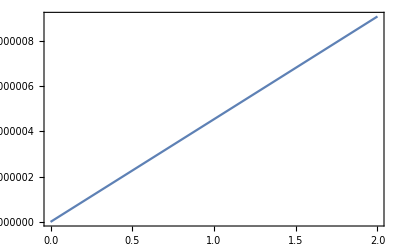
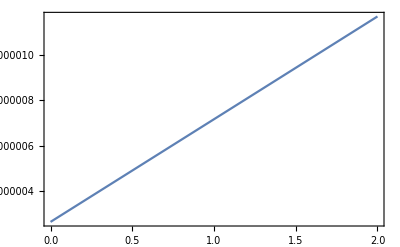
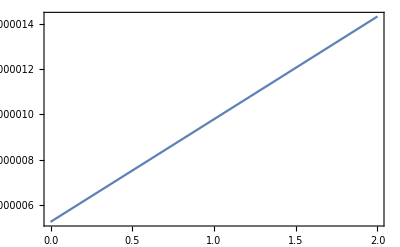

```mathematica
{Plot[EqnSpecTX[xx/mee,1/5,-2],{xx,0,2},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,-1],{xx,0,2},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,0],{xx,0,2},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,1],{xx,0,2},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecTX[xx/mee,1/5,-2],{xx,1}]
```

{xx→0.578856}

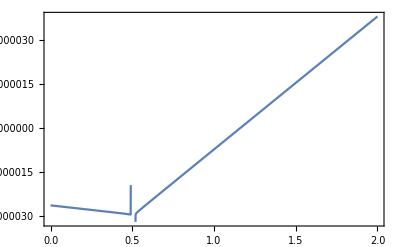
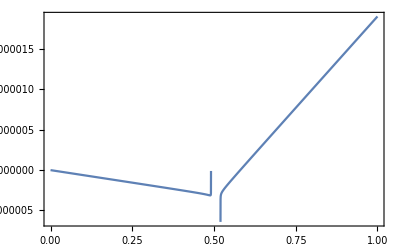
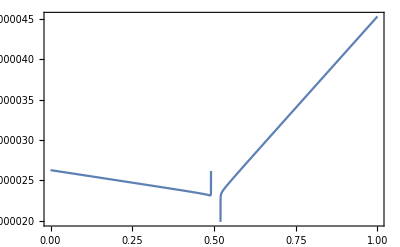
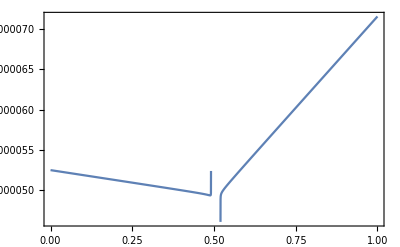

```mathematica
{Plot[EqnSpecTY[xx/mee,1/5,-2],{xx,0,2},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,-1],{xx,0,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,0],{xx,0,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,1],{xx,0,1},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecTY[xx/mee,1/5,-2],{xx,1}]
FindRoot[EqnSpecTY[xx/mee,1/5,-1],{xx,0.6}]
```

{xx→1.159}

{xx→0.580237}

```mathematica
(*есть пик в ближнем ультрафиолете*)
tk0Xm2s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,3.9,4.3,0.005}];
tk0Xm2sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,3.9,4.5,0.005}];
```

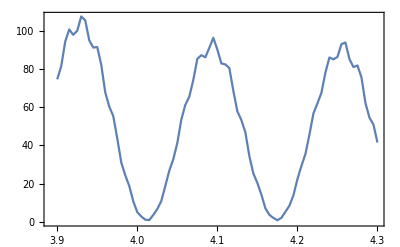
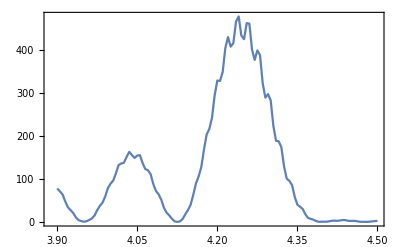

```mathematica
{ListLinePlot[tk0Xm2s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0Xm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*нет пика*)
tk0Ym2s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,8.5,9,0.05}];
tk0Ym2sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,8.5,9,0.05}];
```

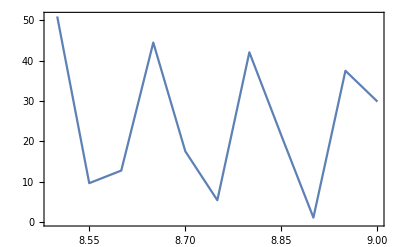
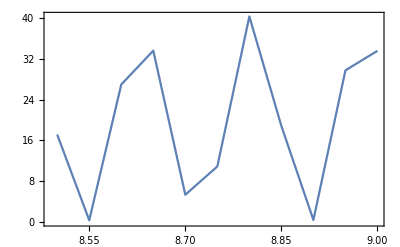

```mathematica
{ListLinePlot[tk0Ym2s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0Ym2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*есть пик в ближнем ультрафиолете*)
tk0Ym1s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,4,4.6,0.05}];
tk0Ym1sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,4,4.6,0.05}];
```

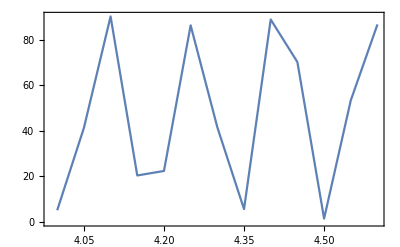
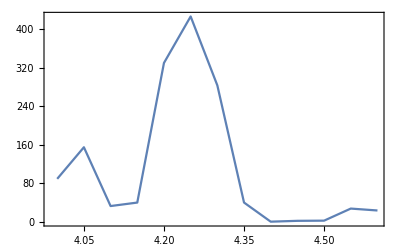

```mathematica
{ListLinePlot[tk0Ym1s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0Ym1sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*нет пика*)
tk0TXm2s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,0.4,0.9,0.05}];
tk0TXm2sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,0.4,0.9,0.05}];
```

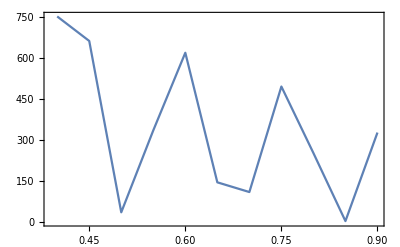
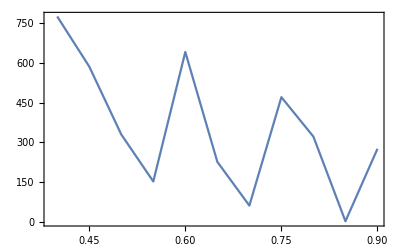

```mathematica
{ListLinePlot[tk0TXm2s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0TXm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*нет пика*)
tk0TYm2s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,1,1.3,0.01}];
tk0TYm2sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,1,1.3,0.01}];
```

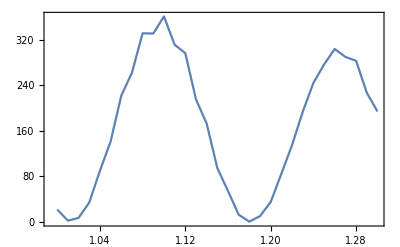
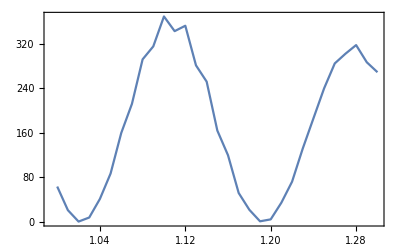

```mathematica
{ListLinePlot[tk0TYm2s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0TYm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*плоский график по np в пике (из уравнения на спектр)*)
```

```mathematica
tnpXm2sm1=ParallelTable[{x,dProbabPlane[-1,4.175123624372432/mee,x,0]},{x,0,0.6,0.005}];
tnpYm1sm1=ParallelTable[{x,dProbabPlane[-1,4.297743995880001/mee,x,0]},{x,0,0.6,0.005}];
tnp=ParallelTable[{x,dProbabPlane[-1,4.255/mee,x,0]},{x,0,0.6,0.005}];
```

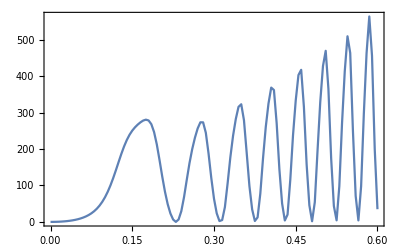
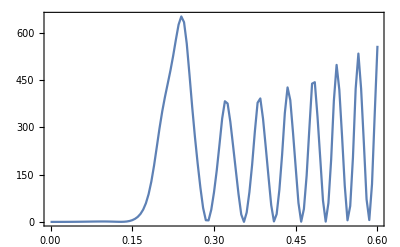
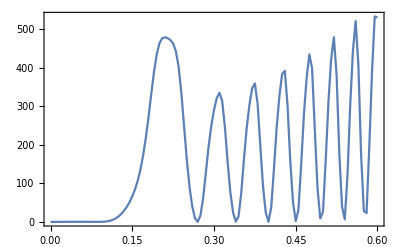

```mathematica
{ListLinePlot[tnpXm2sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tnpYm1sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tnp,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tnp=ParallelTable[{x,dProbabPlane[-1,4.255/mee,x,0]},{x,0,0.6,0.005}];
```

```mathematica
twamp[s_,x_,np_]:=AmplTwistTab[s,x/mee,x * np/mee ][[3]];
twXm2s1 = ParallelTable[{x,dProbabTwist[-2,twamp[1,x,1/5]]},{x,3.8,4.5,0.01}];//AbsoluteTiming
```

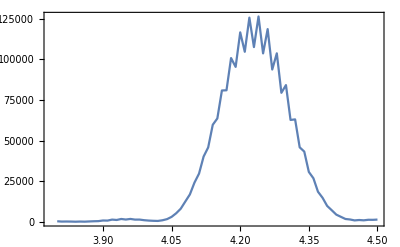

```mathematica
ListLinePlot[twXm2s1,Frame->True,Axes->False,PlotRange->Full]
```